```mathematica
Clear["Global`*"];
```

```mathematica
nX[λ_, T_] := Sqrt[2.4542+0.01125/(λ^2-0.01135)-0.01388 λ^2]-1.8×10^-6(T-293);
nY[λ_, T_] := Sqrt[2.5390+0.01277/(λ^2-0.01189)-0.01849 λ^2-4.3025×10^-5 λ^4-2.9131×10^-5 λ^6]-13.6×10^-6(T-293);
nZ[λ_, T_] := Sqrt[2.5865+0.01310/(λ^2−0.01223)−0.01862 λ^2+4.5778×10^-5 λ^4-3.2526×10^-5 λ^6]−(6.3+2.1 λ)×10^-6(T-293);
```

```mathematica
Manipulate[Plot[{nX[λ, T],nY[λ, T],nZ[λ, T]},{λ,0.4,1.06}],{T,293,338}]
```

```mathematica
nS[λ_,T_]:=nZ[λ,T];
nF[λ_,T_,ϕ_]:= (nX[λ,T] nY[λ,T])/Sqrt[nY[λ,T]^2-(nY[λ,T]^2-nX[λ,T]^2) Cos[ϕ]^2]; (* ϕ - угол к оси ОX *)
```

```mathematica
ϕssf[λ_,T_] := (ϕ/.FindRoot[nS[λ,T]==nF[λ/2,T,ϕ],{ϕ,Pi/4}]);
ϕsff[λ_,T_] := (ϕ/.FindRoot[nS[λ,T]+nF[λ,T,ϕ]==2×nF[λ/2,T,ϕ],{ϕ,Pi/4}]);
```

```mathematica
Δkssf[λ_,T_,ϕ_] := ((2 π)/(λ/2)nF[λ/2,T,ϕ]-2(2 π)/λ nS[λ,T])×10^6;
Δksff[λ_,T_,ϕ_] := ((2 π)/(λ/2)nF[λ/2,T,ϕ]-(2 π)/λ nS[λ,T]-(2 π)/λ nF[λ,T,ϕ])×10^6;
```

```mathematica
λλ=1.064;
TT=293;
```

```mathematica
{180/π ϕssf[λλ,TT],Δkssf[λλ,TT,ϕssf[λλ,TT]]}
```

{11.6034,0.}

```mathematica
{180/π ϕsff[λλ,TT],Δksff[λλ,TT,ϕsff[λλ,TT]]}
```

{48.5375,3.55271×10^-9}

```mathematica
Plot[{Δkssf[λλ,T,ϕssf[λλ,TT]],Δksff[λλ,T,ϕsff[λλ,TT]]},{T,273,313},PlotRange->All];
```

```mathematica
outPowerssf[λ_,T_,L_] := (1-Cos[Δkssf[λ,T,ϕssf[λλ,TT]] L])/(Δkssf[λ,T,ϕssf[λλ,TT]] L)^2;
outPowersff[λ_,T_,L_] := (1-Cos[Δksff[λ,T,ϕsff[λλ,TT]] L])/(Δksff[λ,T,ϕsff[λλ,TT]] L)^2;
```

```mathematica
Plot[outPowerssf[λλ,T,0.02],{T,273,313},PlotRange->All,ImageSize->Large];
```

```mathematica
Plot[outPowersff[λλ,T,0.02],{T,233,353},PlotRange->All,ImageSize->Large];
```

```mathematica
d32 = 0.85×10^-12;
deff = d32×Cos[ϕssf[λλ,TT]];
S=Pi/4 100^2 ×10^-12×10^4;
c=3 10^8×10^2;(*m/s*)
n1[λ_,T_]:=nS[λ, T];
n2[λ_,T_]:=nF[λ/2, T,ϕssf[λλ,TT]];
k1[λ_,T_]:=(2 Pi)/λ n1[λ, T] 10^6;
k2[λ_,T_]:=(2 Pi)/(λ/2) n2[λ, T] 10^6;
σ1[λ_,T_]:=300×(2 Pi k1[λ, T] 2 deff)/n1[λ, T]^2;
σ2[λ_,T_]:=300×(Pi k2[λ, T] 2deff)/n2[λ, T]^2;
Δk[λ_,T_] :=10^-2 ×(k2[λ, T]-2k1[λ, T]);
p0=10×10^7;
```

```mathematica
equations={
A1'[z]== -I σ1[λ, T] A1[z]* A2[z] Exp[-I Δk[λ, T] z],
A2'[z]== -I σ2[λ, T] A1[z]^2 Exp[+I Δk[λ, T] z]
};
startingConditions[P0_] := {
A1[0] == Sqrt[(8 Pi P0)/(c n1[λ, T] S)],
A2[0] == 0
};
```

```mathematica
solution[L_,λvar_,Tvar_, P0_]:=NDSolve[{equations,startingConditions[P0]}/.{λ->λvar,T->Tvar},{A1[z],A2[z]},{z,0,L}];
```

```mathematica
(* Problems with T variation ?!?!?!?! *)
Manipulate[
{Plot[Evaluate[10^-7(c n1[λλ,TT] S)/(8 Pi){Abs[A1[z]],Abs[A2[z]]}^2/.solution[L,λλ,T ,P0 10^7]],{z,0,L},AspectRatio->1,ImageSize->Medium],
ParametricPlot[Evaluate[10^-7((c n1[λλ,TT] S)/(8 Pi)){Re[A2[z]],Im[A2[z]]}/.solution[L,λλ,T,P0 10^7]],{z,0,L},AspectRatio->1,ImageSize->Medium]},
{{L,20},1,100},{{P0,10},1,100},{{T,292},273,313},ContentSize->All]
```

```mathematica
OutPower[L_,T_,P0_]:=10^-7(c n1[λλ,TT] S)/(8 Pi)×((Abs[A2[z]/.solution[L,λλ,T,P0]])/.{z->L})^2;
```

```mathematica
Manipulate[Plot[OutPower[L,T,P0 10^7]/P0,{T,273,313},PlotRange->All],{{L,2},1,10},{{P0,10},1,100}];
```

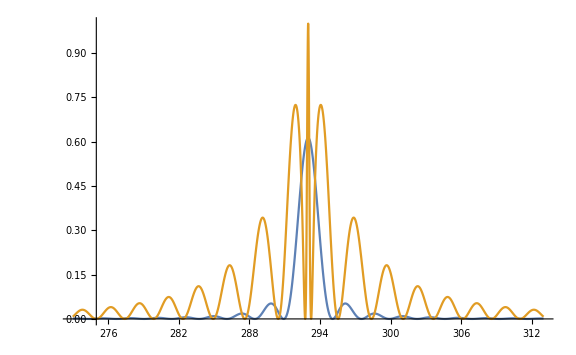

```mathematica
P1 = 5;
dP = 20;
L = 5;
Plot[{OutPower[L,T,P1 10^7]/P1,OutPower[L,T,P1*dP 10^7]/(P1*dP)},{T,273,313},PlotRange->All,ImageSize->Large]
```

```mathematica
Manipulate[Plot[OutPower[L,T,P0 10^7]/P0,{P0,1,50},PlotRange->All],{{T,292},273,313},{{L,2},1,10}];
```